```mathematica
w22 = (1-p)/2 F[x](1-s)(1+δ)/2 M0/(p M0+ (1-p)M[x]); (*Number of mutant male seeds produced by a mutant male parent *)
w12 = (1-p)/2 F[x](1-s)(1-δ)/2 M0/(p M0+ (1-p)M[x]); (*Number of mutant hermaphrodite seeds produced by a mutant male parent *)
w11 =F[xm](s(1-d)+(1-s)/2(((1-p)M[x])/(p M0+ (1-p)M[x])+(p M0)/(p M0+ (1-p)M[x])(1-δ)/2)) + (1-p)/2 F[x](1-s)M[xm]/(p M0+ (1-p)M[x]); (* Number of mutant hermaphrodite seeds produced by a mutant hermaphrodite parent *)
w21 = 1/2 F[xm](1-s)(1+δ)/2(p M0)/(p M0+ (1-p)M[x]); (* Number of mutant male seeds produced by a mutant hermaphrodite parent *)
```

```mathematica
x=.
```

```mathematica
W = 1/(F[x](1-p)(1-s d)){{w11,w12},{w21,w22}};  (*Invasion matrix; term in beginning is the recruitment probability {(# individuals)/(# seeds)} *)
```

```mathematica
W/.sp//Simplify
```

{{((F[xm] (M0-M0 δ+M0 s (3-4 d+δ)+2 (-1+d) s M[x]))/((1-δ+s (1-2 d+δ)) F[x])+(2 M[xm])/(1+δ))/(2 M0),(1-δ)/(2+2 δ)},{(F[xm] (M0 (-1+s) (1+δ)+(2-2 d s) M[x]))/(2 M0 (-1+s (-1+2 d-δ)+δ) F[x]),1/2}}

```mathematica
Wneut=W/. xm-> x//Simplify (*neutrality -> xm = x*)
```

{{(M0 p (1-δ+s (3-4 d+δ))+4 (-1+p) (-1+d s) M[x])/(4 (-1+p) (-1+d s) (M0 p+M[x]-p M[x])),-(M0 (-1+s) (-1+δ))/(4 (-1+d s) (M0 p+M[x]-p M[x]))},{-(M0 p (-1+s) (1+δ))/(4 (-1+p) (-1+d s) (M0 p+M[x]-p M[x])),(M0 (-1+s) (1+δ))/(4 (-1+d s) (M0 p+M[x]-p M[x]))}}

```mathematica
Wneut//Eigenvalues//Simplify
```

{-1/(8 (-1+p) (-1+d s) (M0 p+M[x]-p M[x]))(-M0+M0 s-4 M0 p s+4 d M0 p s-M0 δ+2 M0 p δ+M0 s δ-2 M0 p s δ-4 M[x]+4 p M[x]+4 d s M[x]-4 d p s M[x]+√(M0^2 ((1+δ-2 p δ)^2-2 s ((1+δ)^2-4 p (1+δ) (-1+d+δ)+4 p^2 (-2+2 d+δ^2))+s^2 ((1+δ)^2-4 p (1+δ) (-2+2 d+δ)+4 p^2 (-4 d+4 d^2+δ^2)))-8 M0 (-1+p) (-1+d s) (p (-2+(-2+4 d) s)-(-1+s) (1+δ)) M[x]+16 (-1+p)^2 (-1+d s)^2 M[x]^2)),1/(8 (-1+p) (-1+d s) (M0 p+M[x]-p M[x]))(M0-M0 s+4 M0 p s-4 d M0 p s+M0 δ-2 M0 p δ-M0 s δ+2 M0 p s δ+4 M[x]-4 p M[x]-4 d s M[x]+4 d p s M[x]+√(M0^2 ((1+δ-2 p δ)^2-2 s ((1+δ)^2-4 p (1+δ) (-1+d+δ)+4 p^2 (-2+2 d+δ^2))+s^2 ((1+δ)^2-4 p (1+δ) (-2+2 d+δ)+4 p^2 (-4 d+4 d^2+δ^2)))-8 M0 (-1+p) (-1+d s) (p (-2+(-2+4 d) s)-(-1+s) (1+δ)) M[x]+16 (-1+p)^2 (-1+d s)^2 M[x]^2))}

```mathematica
p1 = (1-p)F[x](1-s)(1+δ)/2(p M0)/(p M0+ (1-p)M[x])1/(F[x](1-p)(1-s d))//Simplify  (*Recursive equation to find the male frequency*)
```

(M0 p (-1+s) (1+δ))/(2 (-1+d s) (M0 p+M[x]-p M[x]))

```mathematica
sp=Solve[p1==p, p][[2]]//Simplify (*at eqm. 2 equilibria- no males in the 1st one*)
```

{p→(M0 (-1+s) (1+δ)+(2-2 d s) M[x])/(2 (-1+d s) (M0-M[x]))}

```mathematica
sp/.s->0/.δ->0/.func/.M0->1
```

{p→-(-1+2 (1-x)^a)/(2 (1-(1-x)^a))}

```mathematica
Wneut/.sp//Eigenvalues //Simplify (*sanity check - eigenvalue of 1 confirms invasion of resident in resident *)
```

{1,(-((-1+d) M0 s (1+δ))+(-1+d s) (-1+δ) M[x])/(M0 (1+δ) (1-δ+s (1-2 d+δ)))}

```mathematica
(*just to get an idea of the male frequency for some values of the parameters*)
```

```mathematica
(M0 (-1+s) (1+δ)+(2-2 d s) M[x])/(2 (-1+d s) (M0-M[x]))/.M -> Function[x, M0 (1-x)^a]/.x->1/2/.a->1/.s->0/.δ->0.2
```

0.2

```mathematica
Solve[Wneut.{q,1-q}== {q,1-q}/. sp,q]//Simplify (* Asymptotic probability of classes *)
```

{{q→(M0 (-1+s (-1+2 d-δ)+δ))/(2 (-1+d s) (M0-M[x]))}}

```mathematica
1-(M0 (-1+s (-1+2 d-δ)+δ))/(2 (-1+d s) (M0-M[x])) == p/. sp //Simplify (*This is because we are working with Wneut, so equilibrium frequencies of any class calculated both ways should be same*)
```

True

```mathematica
Qneut = {q,1-q}/.q->(M0 (-1+s (-1+2 d-δ)+δ))/(2 (-1+d s) (M0-M[x]))
```

{(M0 (-1+s (-1+2 d-δ)+δ))/(2 (-1+d s) (M0-M[x])),1-(M0 (-1+s (-1+2 d-δ)+δ))/(2 (-1+d s) (M0-M[x]))}

```mathematica
Solve[{v1,v2}.{1-p,p}==1, v2][[1]]//Simplify
```

{v2→(1+(-1+p) v1)/p}

{v2→(1-v1+p v1)/p}

```mathematica
V = {v1,v2}
```

{v1,v2}

```mathematica
Solve[V.{1-p,p}==1, v1][[1]]
```

{v1→(-1+p v2)/(-1+p)}

```mathematica
Solve[V.Wneut==V/.v2->(1-v1+p v1)/p/.sp,v1][[1]]//Simplify
```

{v1→((-1+d s) (1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x])}

```mathematica
V = V/.v2->(1-v1+p v1)/p/.v1->((-1+d s) (1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x])/.sp//Simplify
```

{((-1+d s) (1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x]),-((-1+d s) (-1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x])}

```mathematica
V (*normalised reproductive value*)
```

{((-1+d s) (1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x]),-((-1+d s) (-1+δ) (M0-M[x]))/(M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x])}

```mathematica
D[W,xm]/.xm->x
```

{{(((1-d) s+1/2 (1-s) ((M0 p (1-δ))/(2 (M0 p+(1-p) M[x]))+((1-p) M[x])/(M0 p+(1-p) M[x]))) F'[x]+((1-p) (1-s) F[x] M'[x])/(2 (M0 p+(1-p) M[x])))/((1-p) (1-d s) F[x]),0},{(M0 p (1-s) (1+δ) F'[x])/(4 (1-p) (1-d s) F[x] (M0 p+(1-p) M[x])),0}}

```mathematica
selgrad = V.(D[W,xm]/.xm->x).Qneut/.sp//Simplify
```

((-1+s (-1+2 d-δ)+δ) ((M0+M0 δ-M[x]) F'[x]+F[x] M'[x]))/(2 F[x] (M0 (1+δ) (-1+d s+δ-s δ)+(-1+d s) (-1+δ) M[x]))

```mathematica
selgrad/.s->0//Simplify(* similar to the appendix of A model for the gradual evolution of dioecy and heterogametic sex determination-Lessafre 2023*)
```

1/2 (F'[x]/F[x]+M'[x]/(M0+M0 δ-M[x]))

```mathematica
1/2 (F'[x]/F[x]+M'[x]/(M0+M0 δ-M[x]))
```

```mathematica
1/2 (F'[x]/F[x]+M'[x]/(M0+M0 δ-M[x]))/.M -> Function[x, M0 (1-x)^a]/.F -> Function[x, F0 x^b]//Simplify (*Replace functions*)
```

1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ))

```mathematica
x=.
```

```mathematica
npar=.
```

```mathematica
func={M -> Function[x, M0 (1-x)^a],F -> Function[x, F0 x^b]}; (* storing the functions as a rule for convenience*)
```

```mathematica
Solve[1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a))==0,x] (*can't solve anlytically*)
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

0.954993

```mathematica
NSolve[(1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ))/.a->1/2/.b->1/2/.δ->0)==0,x](* x -> 0.30555 for a= 1/2 b = 1/2 δ = 1/5 *)
```

{}

```mathematica
npar = {a->0.95,b->0.95,δ->0,s->0,d->0,M0->1,F0->1}
```

```mathematica
{a->0.95,b->0.95,δ->0,s->0,d->0,M0->1,F0->1}
```

```mathematica
FindRoot[1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ))/.npar,{x,0.3,0,1}]
```

Power::infy: Infinite expression 1/0.^0.05 encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {x} = {1.}.

{0.5→0.676337}

```mathematica
{Δp,selgrad}/.npar
```

{-p+(M0 p (-1+s))/((-1+d s) (M0 p+M[x]-p M[x])),(0.4 (-(1-x)^0.4+p (1-x)^0.4) (-1+x)+0.4 (-1+p) (1-x)^0.4 x)/(2 (-1+p) (p (-1+(1-x)^0.4)-(1-x)^0.4) (-2+(1-x)^0.4) (-1+x) x)}

```mathematica
(*This is to understand the nature of the model 
3 possible outcomes for same a and b values, specefically in this case when hermaphroditism exists acc to Charnov)
i) when δ low - males driven out by herma (Charnov)
  ii) when δ moderate - males herma coexist (as in fig)
     iii) when δ = 1  - males drive pop to extinc (poster and old work)
*)
```

```mathematica
npar={a->0.5,b->0.5,δ-> 0.5, M0->1}; (*storing the parameters as a rule*)
selgrad = V.(D[W,xm]/.xm->x).Qneut/.s->0/.func//Simplify; 
Δp=p1-p /.s->0/.func;
StreamPlot[{Δp,selgrad}/.npar,{p,0,1},{x,0,1}]
```

-Graphics-

```mathematica
p/.sp/.func/.npar/.s->0/.x->0.685//Simplify
```

1.

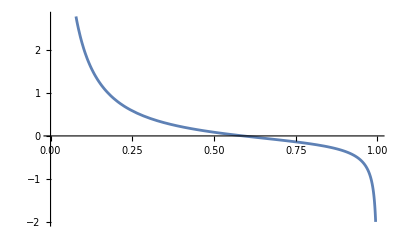

```mathematica
Plot[1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ))/.{a->0.5,b->0.5,δ->0.56,s->0,d->0,M0->1,F0->1},{x,0,1}] (*plotting to assist FindRoot to get sing value*)
```

```mathematica
1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ))/.npar/.x->0.5
```

-0.611795

```mathematica
sp/.s->0/.M -> Function[x, M0 (1-x)^a]/.F -> Function[x, F0 x^b]/.x->1/2/.a->1/2/.δ->1/2//Simplify //N
```

{p→0.146447}

```mathematica
Reduce[(1-2 (1-x)^a+δ)/(2-2 (1-x)^a)>0,δ]
```

((1-x)^a<1&&δ>-1+2 (1-x)^a)||((1-x)^a>1&&δ<-1+2 (1-x)^a)

```mathematica
(1-2 √(1-x)+δ)/(2-2 √(1-x))/.x->0.56/.δ->1/2  (*-ve for a = 1/2 δ = 1/5*)
```

0.257444

```mathematica
δ>-1+2 (1-x)^a/.a->1/2/.δ->1/5/.x->0.3056
```

False

```mathematica
D[1/2 (b/x-(a (1-x)^(-1+a))/(1-(1-x)^a+δ)),x]/.x->0.56/.a->1/2/.b->1/2/.δ->1/2//N (*-ve so convergence stable*)
```

-0.903251

-1.92793

```mathematica
D[(selgrad/.s->0//Simplify),x]
```

1/2 (-F'[x]^2/F[x]^2+M'[x]^2/(M0+M0 δ-M[x])^2+F''[x]/F[x]+M''[x]/(M0+M0 δ-M[x]))

```mathematica
(* Simplifies to 1/2(F''[x]/F[x]+M''[x]/(M0+M0 δ-M[x])) by using condition from equating selgrad to 0*)
```

```mathematica
(*ESS or evo branching?*)
```

```mathematica
Q = Eigenvectors[W/.sp//Simplify][[1]]//Simplify
```

{(M0 F[x]+M0 s F[x]-2 d M0 s F[x]+2 M0 s δ F[x]-2 d M0 s δ F[x]-M0 δ^2 F[x]+M0 s δ^2 F[x]-M0 F[xm]-3 M0 s F[xm]+4 d M0 s F[xm]-4 M0 s δ F[xm]+4 d M0 s δ F[xm]+M0 δ^2 F[xm]-M0 s δ^2 F[xm]+2 s F[xm] M[x]-2 d s F[xm] M[x]+2 s δ F[xm] M[x]-2 d s δ F[xm] M[x]-2 F[x] M[xm]-2 s F[x] M[xm]+4 d s F[x] M[xm]+2 δ F[x] M[xm]-2 s δ F[x] M[xm]+√((1+δ)^2 F[xm]^2 (M0-M0 δ+M0 s (3-4 d+δ)+2 (-1+d) s M[x])^2+(-1+s (-1+2 d-δ)+δ)^2 F[x]^2 (M0+M0 δ-2 M[xm])^2+2 (1+δ) (1-δ+s (1-2 d+δ)) F[x] F[xm] (M[x] (4 M0 (-1+δ)+2 M0 s (1+d+δ-3 d δ)+4 (-1+d) s M[xm])+M0 (M0 (1+δ) (1-δ+s (-5+4 d+δ))+(2-2 δ+s (6-8 d+2 δ)) M[xm]))))/(2 (1+δ) F[xm] (M0 (-1+s) (1+δ)+(2-2 d s) M[x])),1}

```mathematica
(*Is this the leading eigenvector?*)
```

```mathematica
Q = {Q[[1]]/(Q[[1]]+Q[[2]]),Q[[2]]/(Q[[1]]+Q[[2]])}//Simplify (*normalise*)
```

{(M0 F[x]+M0 s F[x]-2 d M0 s F[x]+2 M0 s δ F[x]-2 d M0 s δ F[x]-M0 δ^2 F[x]+M0 s δ^2 F[x]-M0 F[xm]-3 M0 s F[xm]+4 d M0 s F[xm]-4 M0 s δ F[xm]+4 d M0 s δ F[xm]+M0 δ^2 F[xm]-M0 s δ^2 F[xm]+2 s F[xm] M[x]-2 d s F[xm] M[x]+2 s δ F[xm] M[x]-2 d s δ F[xm] M[x]-2 F[x] M[xm]-2 s F[x] M[xm]+4 d s F[x] M[xm]+2 δ F[x] M[xm]-2 s δ F[x] M[xm]+√((1+δ)^2 F[xm]^2 (M0-M0 δ+M0 s (3-4 d+δ)+2 (-1+d) s M[x])^2+(-1+s (-1+2 d-δ)+δ)^2 F[x]^2 (M0+M0 δ-2 M[xm])^2+2 (1+δ) (1-δ+s (1-2 d+δ)) F[x] F[xm] (M[x] (4 M0 (-1+δ)+2 M0 s (1+d+δ-3 d δ)+4 (-1+d) s M[xm])+M0 (M0 (1+δ) (1-δ+s (-5+4 d+δ))+(2-2 δ+s (6-8 d+2 δ)) M[xm]))))/(M0 F[x]+M0 s F[x]-2 d M0 s F[x]+2 M0 s δ F[x]-2 d M0 s δ F[x]-M0 δ^2 F[x]+M0 s δ^2 F[x]-3 M0 F[xm]-M0 s F[xm]+4 d M0 s F[xm]-4 M0 δ F[xm]+4 d M0 s δ F[xm]-M0 δ^2 F[xm]+M0 s δ^2 F[xm]+4 F[xm] M[x]+2 s F[xm] M[x]-6 d s F[xm] M[x]+4 δ F[xm] M[x]+2 s δ F[xm] M[x]-6 d s δ F[xm] M[x]-2 F[x] M[xm]-2 s F[x] M[xm]+4 d s F[x] M[xm]+2 δ F[x] M[xm]-2 s δ F[x] M[xm]+√((1+δ)^2 F[xm]^2 (M0-M0 δ+M0 s (3-4 d+δ)+2 (-1+d) s M[x])^2+(-1+s (-1+2 d-δ)+δ)^2 F[x]^2 (M0+M0 δ-2 M[xm])^2+2 (1+δ) (1-δ+s (1-2 d+δ)) F[x] F[xm] (M[x] (4 M0 (-1+δ)+2 M0 s (1+d+δ-3 d δ)+4 (-1+d) s M[xm])+M0 (M0 (1+δ) (1-δ+s (-5+4 d+δ))+(2-2 δ+s (6-8 d+2 δ)) M[xm])))),(2 (1+δ) F[xm] (M0 (-1+s) (1+δ)+(2-2 d s) M[x]))/(M0 F[x]+M0 s F[x]-2 d M0 s F[x]+2 M0 s δ F[x]-2 d M0 s δ F[x]-M0 δ^2 F[x]+M0 s δ^2 F[x]-3 M0 F[xm]-M0 s F[xm]+4 d M0 s F[xm]-4 M0 δ F[xm]+4 d M0 s δ F[xm]-M0 δ^2 F[xm]+M0 s δ^2 F[xm]+4 F[xm] M[x]+2 s F[xm] M[x]-6 d s F[xm] M[x]+4 δ F[xm] M[x]+2 s δ F[xm] M[x]-6 d s δ F[xm] M[x]-2 F[x] M[xm]-2 s F[x] M[xm]+4 d s F[x] M[xm]+2 δ F[x] M[xm]-2 s δ F[x] M[xm]+√((1+δ)^2 F[xm]^2 (M0-M0 δ+M0 s (3-4 d+δ)+2 (-1+d) s M[x])^2+(-1+s (-1+2 d-δ)+δ)^2 F[x]^2 (M0+M0 δ-2 M[xm])^2+2 (1+δ) (1-δ+s (1-2 d+δ)) F[x] F[xm] (M[x] (4 M0 (-1+δ)+2 M0 s (1+d+δ-3 d δ)+4 (-1+d) s M[xm])+M0 (M0 (1+δ) (1-δ+s (-5+4 d+δ))+(2-2 δ+s (6-8 d+2 δ)) M[xm]))))}

```mathematica
Q[[1]] + Q[[2]]//Simplify
```

1

```mathematica
Hw = V.D[D[W,xm],xm].Qneut/.sp/.s->0/.xm->x/.M -> Function[x, M0 (1-x)^a]/.F -> Function[x, F0 x^b]//Simplify (*refer to Charles Mullon 2023 for this*)
```

1/2 (-b/x^2+b^2/x^2-((-1+a) a (1-x)^(-2+a))/(-1+(1-x)^a-δ))

```mathematica
Hq = V.D[W,xm].Q/.sp/.s->0/.xm->x/.M -> Function[x, M0 (1-x)^a]/.F -> Function[x, F0 x^b]//Simplify
```

-((-1+(1-x)^a) (a (1-x)^a x-b (-1+x) (-1+(1-x)^a-δ)) (F0 M0 (1-x)^a x^b (-1+δ)+√(F0^2 M0^2 x^(2 b) (-1+δ)^2 (1-(1-x)^a+δ)^2)))/((-1+x) x (-1+(1-x)^a-δ) (-1+δ) (√(F0^2 M0^2 x^(2 b) (-1+δ)^2 (1-(1-x)^a+δ)^2)+F0 M0 x^b (-1+(1-x)^a+(-2+3 (1-x)^a) δ-δ^2)))

```mathematica
Hw + 2 Hq /.x->0.56/.a->1/2/.b->1/2/.δ->1/2/.F0->1/.M0->1//Simplify
```

-0.905054

```mathematica
sp/.M -> Function[x, M0 (1-x)^a]/.F -> Function[x, F0 x^b]/.s->0//Simplify
```

{p→(1-2 (1-x)^a+δ)/(2-2 (1-x)^a)}

```mathematica
(*What abt the eqm with only herma?*)
```

```mathematica
sp=Solve[p1==p, p][[1]]//Simplify
```

{p→0}

```mathematica
Wneut/.sp//Eigenvalues //Simplify
```

{(M0 (-1+s) (1+δ))/(4 (-1+d s) M[x]),1}

```mathematica
(* sanity check - one of the eigenvalues is 1, what about the other?*)
```

```mathematica
(M0 (-1+s) (1+δ))/(4 (-1+d s) M[x])/.M->Function[x, M0 (1-x)^a]//Simplify
```

((-1+s) (1-x)^-a (1+δ))/(4 (-1+d s))

```mathematica
Solve[Wneut.{q,1-q}== {q,1-q}/. sp,q]//Simplify
```

{{q→1}}

```mathematica
Qneut = {q,1-q}/.%[[1]]
```

{1,0}

```mathematica
Solve[V.Wneut==V/.v1->(-1+p v2)/(-1+p)/.sp,v2][[1]]//Simplify
```

{v2→(M0 (-1+s) (-1+δ))/(M0 (-1+s) (1+δ)+(4-4 d s) M[x])}

```mathematica
V=V/.v1->(-1+p v2)/(-1+p)/.v2->(M0 (-1+s) (-1+δ))/(M0 (-1+s) (1+δ)+(4-4 d s) M[x])/.sp//Simplify
```

{1,(M0 (-1+s) (-1+δ))/(M0 (-1+s) (1+δ)+(4-4 d s) M[x])}

```mathematica
D[W,xm]/.xm->x
```

{{(((1-d) s+1/2 (1-s) ((M0 p (1-δ))/(2 (M0 p+(1-p) M[x]))+((1-p) M[x])/(M0 p+(1-p) M[x]))) F'[x]+((1-p) (1-s) F[x] M'[x])/(2 (M0 p+(1-p) M[x])))/((1-p) (1-d s) F[x]),0},{(M0 p (1-s) (1+δ) F'[x])/(4 (1-p) (1-d s) F[x] (M0 p+(1-p) M[x])),0}}

```mathematica
selgrad = V.(D[W,xm]/.xm->x).Qneut/.sp//Simplify
```

((-1+(-1+2 d) s) M[x] F'[x]+(-1+s) F[x] M'[x])/(2 (-1+d s) F[x] M[x])

```mathematica
selgrad/.s->0//Simplify
```

1/2 (F'[x]/F[x]+M'[x]/M[x])

```mathematica
(*Exactly same result as Thomas's paper --> This gives x^* =  b/(a+b)*)
```

```mathematica
(*So need to check when can males invade and stay in the hermaphrodite population*)
```

```mathematica
w = 1/(F[x](1-d s))  F[x](1-s)(1+δ)/2 M0/M[x]; (* males prodeuced by rare mutant males*)
```

```mathematica
w/.M->Function[x, M0 (1-x)^a]/.s->0//Simplify
```

1/2 (1-x)^-a (1+δ)

```mathematica
(*male invasion when (1+δ)/(1-x)^a>2*)
```

```mathematica
3/2*2^(1/2)//N
```

2.12132

```mathematica
1/2 (1-x)^-a (1+δ)/.a->1/2/.x->1/2
```

(1+δ)/(√2)

```mathematica
√2-1//N
```

0.414214

```mathematica
(* sex allocation evolution in a DSI pop*)
```

4 classes
Ha - (m)  (s)   p1
Hb - (m)  (S)   p2
Ma - (M)  (s)   p3
Mb - (M)  (S)   p1

```mathematica
(*Writing invasion matrix*)
```

```mathematica
p1 =.;
```

```mathematica
Ra = p2 M[x] + p3 M0 + p4 M0; (*compatible pollens for Ha *)
Rb = p1 M[x] + p3 M0 + p4 M0;
```

```mathematica
w11 = F[xm] 1/2(1/2 p2 M[x] + 1/2 p3 M0 + 1/4 p4 M0)/Ra + p2 F[x] 1/2 (1/2 M[xm])/Rb;
w12 = F[xm] 1/2(1/2 p1 M[x] + 1/2 p3 M0 (1-δ)/2)/Rb + p1 F[x] 1/2 (1/2 M[xm])/Ra;
w13 =p1 F[x] 1/2 (1/2 M0)/Ra + p2 F[x] 1/2 (1/2 M0 (1-δ)/2)/Rb;
w14 =p1 F[x] 1/2 (1/4 M0)/Ra;
w21 = F[xm] 1/2(1/2 p2 M[x] +  1/4 p4 M0)/Ra + p2 F[x] 1/2 (1/2 M[xm])/Rb;
w22 = F[xm] 1/2(1/2 p1 M[x] + 1/2 p3 M0 (1-δ)/2 + p4 M0 (1-δ)/2)/Rb + p1 F[x] 1/2 (1/2 M[xm])/Ra;
w23 = p2 F[x] 1/2 (1/2 M0 (1-δ)/2)/Rb;
w24 = p1 F[x] 1/2 (1/4 M0)/Ra + p2 F[x] 1/2 (M0 (1-δ)/2)/Rb;
w31 = F[xm] 1/2(1/2 p3 M0 + 1/4 p4 M0)/Ra;
w32 = F[xm] 1/2(1/2 p3 M0 (1+δ)/2)/Rb;
w33 =  p1 F[x] 1/2 (1/2 M0)/Ra + p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w34 = p1 F[x] 1/2 (1/4 M0)/Ra;
w41 =  F[xm] 1/2(1/4 p4 M0)/Ra;
w42 = F[xm] 1/2(1/2 p3 M0 (1+δ)/2 +  p4 M0 (1+δ)/2)/Rb;
w43 =  p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w44 =  p1 F[x] 1/2 (1/4 M0)/Ra + p2 F[x] 1/2 (M0 (1+δ)/2)/Rb;
```

```mathematica
W = 1/(F[x](p1 + p2)){{w11,w12,w13,w14},{w21,w22,w23,w24},{w31,w32,w33,w34},{w41,w42,w43,w44}};(*Invasion matrix; *)
```

```mathematica
Wneut = W/.xm->x;
```

```mathematica
Wneut/.func
```

{{(x^-b ((F0 ((M0 p3)/2+(M0 p4)/4+1/2 M0 p2 (1-x)^a) x^b)/(2 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 (1-x)^a x^b)/(4 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(x^-b ((F0 M0 p1 (1-x)^a x^b)/(4 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 x^b (1/2 M0 p1 (1-x)^a+1/4 M0 p3 (1-δ)))/(2 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(x^-b ((F0 M0 p1 x^b)/(4 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 x^b (1-δ))/(8 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+M0 p2 (1-x)^a))},{(x^-b ((F0 ((M0 p4)/4+1/2 M0 p2 (1-x)^a) x^b)/(2 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 (1-x)^a x^b)/(4 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(x^-b ((F0 M0 p1 (1-x)^a x^b)/(4 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 x^b (1/2 M0 p1 (1-x)^a+1/4 M0 p3 (1-δ)+1/2 M0 p4 (1-δ)))/(2 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(M0 p2 (1-δ))/(8 (p1+p2) (M0 p3+M0 p4+M0 p1 (1-x)^a)),(x^-b ((F0 M0 p1 x^b)/(8 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 x^b (1-δ))/(4 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2))},{((M0 p3)/2+(M0 p4)/4)/(2 (p1+p2) (M0 p3+M0 p4+M0 p2 (1-x)^a)),(M0 p3 (1+δ))/(8 (p1+p2) (M0 p3+M0 p4+M0 p1 (1-x)^a)),(x^-b ((F0 M0 p1 x^b)/(4 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 x^b (1+δ))/(8 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2)),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+M0 p2 (1-x)^a))},{(M0 p4)/(8 (p1+p2) (M0 p3+M0 p4+M0 p2 (1-x)^a)),(1/4 M0 p3 (1+δ)+1/2 M0 p4 (1+δ))/(2 (p1+p2) (M0 p3+M0 p4+M0 p1 (1-x)^a)),(M0 p2 (1+δ))/(8 (p1+p2) (M0 p3+M0 p4+M0 p1 (1-x)^a)),(x^-b ((F0 M0 p1 x^b)/(8 (M0 p3+M0 p4+M0 p2 (1-x)^a))+(F0 M0 p2 x^b (1+δ))/(4 (M0 p3+M0 p4+M0 p1 (1-x)^a))))/(F0 (p1+p2))}}

```mathematica
Eigenvalues[Wneut]//Simplify
```

```mathematica
np3 = (p1 F[x] 1/2(p3 M0 + 1/2 p4 M0)/Ra+p2 F[x](1+δ)/2(1/2 p3 M0)/Rb )1/(F[x](p1 + p2))/.p2->1-p1-p3-p4/.func//Simplify  ;
np4 = (p1 F[x] 1/2(1/2 p4 M0)/Ra+p2 F[x](1+δ)/2(1/2 p3 M0 +p4 M0)/Rb )1/(F[x](p1 + p2))/.p2->1-p1-p3-p4/.func//Simplify  ;
np1 = (p1 F[x](1/2 p2 M[x]+1/2 p3 M0 +1/4 p4 M0)/Ra+p2 F[x](1/2 p1 M[x]+(1-δ)/4 p3 M0)/Rb )1/(F[x](p1 + p2))/.p2->1-p1-p3-p4/.func//Simplify  ;
np2 = (p1 F[x](1/2 p2 M[x]+1/4 p4 M0)/Ra+p2 F[x](1/2 p1 M[x]+(1-δ)/4 p3 M0 +(1-δ)/2 p4 M0)/Rb )1/(F[x](p1 + p2))/.p2->1-p1-p3-p4/.func//Simplify  ;
```

```mathematica
npar={a->1,b->1,δ-> 1, M0->1,F0->1};
```

```mathematica
np1/.npar/.x->0.25//Simplify
```

-(-(1.5 p1 (-1+p1+p3+p4))/(0.75 p1+p3+p4)+(p1 (2 p3+p4-1.5 (-1+p1+p3+p4)))/(p3+p4-0.75 (-1+p1+p3+p4)))/(4 (-1+p3+p4))

```mathematica
np1+np3+np4+ np2//Simplify
```

1

```mathematica
Collect[{v1,v2,v3,v4}.D[W,xm].{p1,1-p1-p3-p4,p3,p4}/.xm->x,F'[x]]/.func/.a->1/.b->1//Simplify
```

(p1 (2 p3+p4) v3 (p1+p3+p4-p1 x)+p1 p4 v4 (p1+p3+p4-p1 x)+p1 v2 (p4-2 p2 (-1+x)) (p1+p3+p4-p1 x)+p1 v1 (2 p3+p4-2 p2 (-1+x)) (p1+p3+p4-p1 x)+2 p1 (-1+p1+p3+p4) v1 x (p1+p3+p4-p1 x)+2 p1 (-1+p1+p3+p4) v2 x (p1+p3+p4-p1 x)-2 p1 p2 v1 x (p2+p3+p4-p2 x)-2 p1 p2 v2 x (p2+p3+p4-p2 x)+(-1+p1+p3+p4) v1 (p2+p3+p4-p2 x) (2 p1 (-1+x)+p3 (-1+δ))+(-1+p1+p3+p4) v2 (p2+p3+p4-p2 x) (2 p1 (-1+x)+(p3+2 p4) (-1+δ))-p3 (-1+p1+p3+p4) v3 (p2+p3+p4-p2 x) (1+δ)-(-1+p1+p3+p4) (p3+2 p4) v4 (p2+p3+p4-p2 x) (1+δ))/(8 (p1+p2) x (p1+p3+p4-p1 x) (p2+p3+p4-p2 x))

```mathematica
npar = {δ->1,a->1, b->1,  M0->1, F0->1};
numsols = NSolve[({np3-p3,np4-p4,np1-p1}=={0,0,0}/.x->1/2/.func/.npar),{p1,p3,p4}] (*can't find analytically*)
```

{{p4→1.05782,p3→-3.07465,p1→-0.83523},{p4→-0.465432+0.18223 ⅈ,p3→0.255731-0.286502 ⅈ,p1→0.776039+0.316405 ⅈ},{p4→-0.465432+0.18223 ⅈ,p3→0.255731-0.286502 ⅈ,p1→0.776039+0.316405 ⅈ},{p4→-0.465432-0.18223 ⅈ,p3→0.255731+0.286502 ⅈ,p1→0.776039-0.316405 ⅈ},{p4→-0.465432+0.18223 ⅈ,p3→0.255731-0.286502 ⅈ,p1→0.776039+0.316405 ⅈ},{p4→-0.465432+0.18223 ⅈ,p3→0.255731-0.286502 ⅈ,p1→0.776039+0.316405 ⅈ},{p4→2.29551,p3→-1.07426,p1→0.361866},{p4→0,p3→0,p1→0.5},{p4→0,p3→0,p1→0.5},{p4→-0.3+0.1 ⅈ,p3→0.3-0.1 ⅈ,p1→0.6-0.2 ⅈ},{p4→-0.3-0.1 ⅈ,p3→0.3+0.1 ⅈ,p1→0.6+0.2 ⅈ},{p4→-0.3+0.1 ⅈ,p3→0.3-0.1 ⅈ,p1→0.6-0.2 ⅈ},{p4→-0.3+0.1 ⅈ,p3→0.3-0.1 ⅈ,p1→0.6-0.2 ⅈ},{p4→-0.3+0.1 ⅈ,p3→0.3-0.1 ⅈ,p1→0.6-0.2 ⅈ},{p4→-0.3-0.1 ⅈ,p3→0.3+0.1 ⅈ,p1→0.6+0.2 ⅈ},{p4→-0.3-0.1 ⅈ,p3→0.3+0.1 ⅈ,p1→0.6+0.2 ⅈ},{p4→0.244204,p3→0.304123,p1→0.310176},{p4→0,p3→0.5,p1→0.5},{p4→0,p3→0.5,p1→0.5}}

```mathematica
numsols[[17]]
```

{p4→0.244204,p3→0.304123,p1→0.310176}

{{0.5,0.323374,0.242977,0.121488},{0.29978,0.323374,0,0.121488},{0.306118,0.176626,0.371488,0.121488},{0.105898,0.550299,0.128512,0.378512}}

```mathematica
Eigenvalues[(Wneut/.p2->1-p1-p3-p4/.func/.npar/.x->1/2/.numsols[[6]])]//Simplify
```

{1.,0.335541,0.237833,3.33455×10^-16}

```mathematica
Reduce[(Wneut/.func/.npar/.p2->1-p1-p3-p4/.numsols[[8]]).{q1,1-q1-q3-q4,q3,q4}=={q1,1-q1-q3-q4,q3,q4},{q1,q3,q4}]//Simplify (* Asymptotic probability of classes*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x==0.5&&q1==0.303466&&q3==0.250066&&q4==0.264522

```mathematica
Qneut = {p1,1-p1-p3-p4,p3,p4}/.numsols[[6]]
```

{0.303466,0.181946,0.250066,0.264522}

```mathematica
v1=.
```

```mathematica
V= {v1,v2,v3,v4};
```

```mathematica
NSolve[Qneut.V==1,v1][[1]]//Simplify
```

{v1→3.29526-0.599559 v2-0.824031 v3-0.871669 v4}

```mathematica
npar
```

{δ→1,a→1/2,b→1/2,M0→1,F0→1}

```mathematica
Solve[V.(Wneut/.p2->1-p1-p3-p4/.func/.npar/.x->1/2/.numsols[[6]])==V/.Solve[Qneut.V==1,v1][[1]],{v2,v3,v4}]//Simplify
```

{}

```mathematica
Wneut/.p2->1-p1-p3-p4/.func/.npar/.x->1/2/.numsols[[17]]
```

{{0.5,0.260694,0.277319,0.13866},{0.228092,0.260694,0,0.13866},{0.381075,0.239306,0.38866,0.13866},{0.109168,0.62362,0.11134,0.36134}}

```mathematica
V = {v1,v2,v3,v4}
```

{v1,v2,v3,v4}

```mathematica
NSolve
```

```mathematica
V =V/.Solve[Qneut.V==1,v1][[1]]/.Solve[V.(Wneut/.p2->1-p1-p3-p4/.func/.npar/.x->1/2/.numsols[[6]])==V/.Solve[Qneut.V==1,v1][[1]],{v2,v3,v4}][[1]]//Simplify
```

{1.35966,1.35966,0.660731,0.660731}

```mathematica
(* more reproductive value for hermaphrodites than males *)
```

```mathematica
selgrad =  V.(D[W,xm]/.xm->x).Qneut/.p2->1-p1-p3-p4/.func/.npar/.numsols[[6]]//Simplify
```

(1.27222+1.39405 √(1-x)+(-1.99291-0.67983 √(1-x)) x)/(x (4.52394+5.79585 √(1-x)-4.52394 x-1. √(1-x) x))

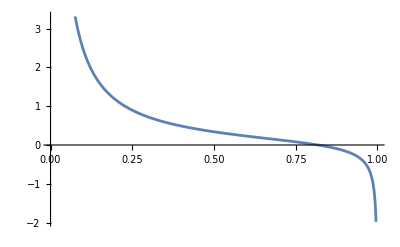

```mathematica
Plot[selgrad,{x,0,1}]
```

```mathematica
(*although this shows that selgrad vanishes around 0.8, it does not mean that we can equate it to 0. 
Because this sel grad is using frequencies when x = 1/2. So, we can only introduce mutants very close to x = 1/2. To do this we need to follow the numerical method in 
Thomas's paper where he uses iteration to find the singular strategies. Basically need to iterate both the frequencies and the trait  *)
```

```mathematica
singstrat = NSolve[selgrad==0,x][[1]] (* not correct*)
```

{x→0.817847}

```mathematica
npar = {δ->1,a->1/2, b->1/2,  M0->1, F0->1};
numsols = NSolve[({np3-p3,np4-p4,np1-p1}=={0,0,0}/.singstrat/.func/.npar),{p1,p3,p4}]
```

{{p4→-0.393915+0.165911 ⅈ,p3→0.23433-0.251945 ⅈ,p1→0.755116+0.318447 ⅈ},{p4→-0.393915-0.165911 ⅈ,p3→0.23433+0.251945 ⅈ,p1→0.755116-0.318447 ⅈ},{p4→1.09055,p3→-2.73331,p1→-0.952535},{p4→0,p3→0,p1→0.5},{p4→0,p3→0,p1→0.5},{p4→0,p3→0,p1→0.5},{p4→0,p3→0,p1→0.5},{p4→0,p3→0,p1→0.5},{p4→2.44541,p3→-1.19785,p1→0.451286},{p4→2.44541,p3→-1.19785,p1→0.451286},{p4→-0.307944-0.0722975 ⅈ,p3→0.307944+0.0722975 ⅈ,p1→0.606221+0.239541 ⅈ},{p4→-0.307944+0.0722975 ⅈ,p3→0.307944-0.0722975 ⅈ,p1→0.606221-0.239541 ⅈ},{p4→-0.307944-0.0722975 ⅈ,p3→0.307944+0.0722975 ⅈ,p1→0.606221+0.239541 ⅈ},{p4→-0.307944-0.0722975 ⅈ,p3→0.307944+0.0722975 ⅈ,p1→0.606221+0.239541 ⅈ},{p4→-0.307944-0.0722975 ⅈ,p3→0.307944+0.0722975 ⅈ,p1→0.606221+0.239541 ⅈ},{p4→-0.307944+0.0722975 ⅈ,p3→0.307944-0.0722975 ⅈ,p1→0.606221-0.239541 ⅈ},{p4→-0.307944+0.0722975 ⅈ,p3→0.307944-0.0722975 ⅈ,p1→0.606221-0.239541 ⅈ},{p4→0.229661,p3→0.325277,p1→0.317862},{p4→0,p3→0.5,p1→0.5}}

```mathematica
(*streamplot to get an idea about the outcomes of the model*)
```

Part::partd: Part specification 0.250066⟦4⟧ is longer than depth of object.

0.250066⟦4⟧

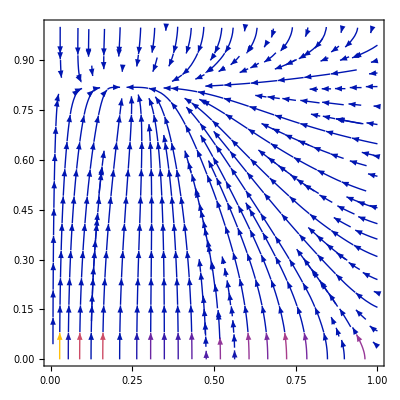

```mathematica
npar= {δ->1,a->1/2, b->1/2,  M0->1, F0->1};(*storing the parameters as a rule*)
(*selgrad = V.(D[W,xm]/.xm->x).Qneut/.p2->1-p1-p3-p4/.func/.npar/.numsols[[6]]//Simplify;*)
Δp1=np1-p1 /.func/.npar/.p3->Qneut[[3]]/.p4->Qneut[[4]];
Δp3=np3-p3 /.func/.npar/.p1->Qneut[[1]]/.p4->Qneut[[4]];
Δp4=np4-p4 /.func/.npar/.p3->Qneut[[3]]/.p1->Qneut[[1]];
StreamPlot[{Δp1,selgrad}/.npar,{p1,0,1},{x,0,1}]
```

```mathematica
(*Which of these equilibria are stable?*)
```

```mathematica
(* M invasion in m*) (*finish this part*)
```

```mathematica
w11 =  p1 F[x] 1/2 (1/2 M0)/Ra + p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w12 = p1 F[x] 1/2 (1/4 M0)/Ra;
w21 =  p2 F[x] 1/2 (1/2 M0 (1+δ)/2)/Rb;
w22 =  p1 F[x] 1/2 (1/4 M0)/Ra + p2 F[x] 1/2 (M0 (1+δ)/2)/Rb;
```

```mathematica
(*Iterative Numerical simulations *)
```

```mathematica
W
```

{{((F[xm] ((M0 p3)/2+(M0 p4)/4+1/2 p2 M[x]))/(2 (M0 p3+M0 p4+p2 M[x]))+(p2 F[x] M[xm])/(4 (M0 p3+M0 p4+p1 M[x])))/((p1+p2) F[x]),((F[xm] (1/4 M0 p3 (1-δ)+1/2 p1 M[x]))/(2 (M0 p3+M0 p4+p1 M[x]))+(p1 F[x] M[xm])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),((M0 p2 (1-δ) F[x])/(8 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+p2 M[x]))},{((F[xm] ((M0 p4)/4+1/2 p2 M[x]))/(2 (M0 p3+M0 p4+p2 M[x]))+(p2 F[x] M[xm])/(4 (M0 p3+M0 p4+p1 M[x])))/((p1+p2) F[x]),((F[xm] (1/4 M0 p3 (1-δ)+1/2 M0 p4 (1-δ)+1/2 p1 M[x]))/(2 (M0 p3+M0 p4+p1 M[x]))+(p1 F[x] M[xm])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p2 (1-δ))/(8 (p1+p2) (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1-δ) F[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(8 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x])},{(((M0 p3)/2+(M0 p4)/4) F[xm])/(2 (p1+p2) F[x] (M0 p3+M0 p4+p2 M[x])),(M0 p3 (1+δ) F[xm])/(8 (p1+p2) F[x] (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1+δ) F[x])/(8 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+p2 M[x]))},{(M0 p4 F[xm])/(8 (p1+p2) F[x] (M0 p3+M0 p4+p2 M[x])),((1/4 M0 p3 (1+δ)+1/2 M0 p4 (1+δ)) F[xm])/(2 (p1+p2) F[x] (M0 p3+M0 p4+p1 M[x])),(M0 p2 (1+δ))/(8 (p1+p2) (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1+δ) F[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(8 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x])}}

```mathematica
Wneut
```

{{((p2 F[x] M[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(F[x] ((M0 p3)/2+(M0 p4)/4+1/2 p2 M[x]))/(2 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),((F[x] (1/4 M0 p3 (1-δ)+1/2 p1 M[x]))/(2 (M0 p3+M0 p4+p1 M[x]))+(p1 F[x] M[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),((M0 p2 (1-δ) F[x])/(8 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+p2 M[x]))},{((p2 F[x] M[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(F[x] ((M0 p4)/4+1/2 p2 M[x]))/(2 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),((F[x] (1/4 M0 p3 (1-δ)+1/2 M0 p4 (1-δ)+1/2 p1 M[x]))/(2 (M0 p3+M0 p4+p1 M[x]))+(p1 F[x] M[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p2 (1-δ))/(8 (p1+p2) (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1-δ) F[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(8 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x])},{((M0 p3)/2+(M0 p4)/4)/(2 (p1+p2) (M0 p3+M0 p4+p2 M[x])),(M0 p3 (1+δ))/(8 (p1+p2) (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1+δ) F[x])/(8 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(4 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x]),(M0 p1)/(8 (p1+p2) (M0 p3+M0 p4+p2 M[x]))},{(M0 p4)/(8 (p1+p2) (M0 p3+M0 p4+p2 M[x])),(1/4 M0 p3 (1+δ)+1/2 M0 p4 (1+δ))/(2 (p1+p2) (M0 p3+M0 p4+p1 M[x])),(M0 p2 (1+δ))/(8 (p1+p2) (M0 p3+M0 p4+p1 M[x])),((M0 p2 (1+δ) F[x])/(4 (M0 p3+M0 p4+p1 M[x]))+(M0 p1 F[x])/(8 (M0 p3+M0 p4+p2 M[x])))/((p1+p2) F[x])}}

```mathematica
npar= {δ->1,a->1, b->1,  M0->1, F0->1};(*storing the parameters as a rule*)
```

```mathematica
findP[x_]:=FindRoot[({np3==p3,np4==p4,np1==p1}/.npar),{{p1,0.5,0,1},{p3,0.5,0,1},{p4,0.5,0,1}}]
```

```mathematica
findP[0.5]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity,ComplexInfinity,ComplexInfinity} is not a list of numbers with dimensions {3} at {p1,p3,p4} = {0.5,0.5,0.5}.

FindRoot[{np3==p3,np4==p4,np1==p1}/.npar,{{p1,0.5,0,1},{p3,0.5,0,1},{p4,0.5,0,1}}]

```mathematica
({np1,np3,np4}/.npar/.x->0.5)
```

{-(-(1. p1 (-1+p1+p3+p4))/(0.5 p1+p3+p4)+(p1 (2 p3+p4-1. (-1+p1+p3+p4)))/(p3+p4-0.5 (-1+p1+p3+p4)))/(4 (-1+p3+p4)),-(-(2 p3 (-1+p1+p3+p4))/(0.5 p1+p3+p4)+(p1 (2 p3+p4))/(p3+p4-0.5 (-1+p1+p3+p4)))/(4 (-1+p3+p4)),-(-(2 (-1+p1+p3+p4) (p3+2 p4))/(0.5 p1+p3+p4)+(p1 p4)/(p3+p4-0.5 (-1+p1+p3+p4)))/(4 (-1+p3+p4))}

```mathematica
FindRoot[({np1,np3,np4}/.npar/.x->0.5) == {p1,p3,p4},{{p1,0.2,0,1},{p3,0.5,0,1},{p4,0.3,0,1}}]
```

FindRoot::reged: The point {2.45904×10^-18,0.,0.990521} is at the edge of the search region {0.,1.} in coordinate 2 and the computed search direction points outside the region.

{p1→2.45904×10^-18,p3→0.,p4→0.990521}

```mathematica
iterate[x0_,eps_,tol_,maxIter_]:= Module[{x=x0,pVals,p1,p2,p3,p4,xNew},
Table[
pVals=findP[x];
If[pVals=={},Return[{}]];
{p1,p2,p3,p4}={p1,1-p1-p3-p4,p3,p4}/. pVals;
Qneut = {p1,p2,p3,p4}
V = {v1,v2,v3,v4}
Solve[

xNew=x+eps*S[x];
If[Abs[xNew-x]<tol,Return[xNew]];
x=xNew,{maxIter}]]
```

Solving V

```mathematica
Qneut = {0.35,0.125,0.25,0.275}
```

{0.35,0.125,0.25,0.275}

```mathematica
V = {v1,v2,v3,v4};
```

```mathematica
NSolve[Qneut.V == 1,v1][[1]]//Simplify
```

{v1→2.85714-0.357143 v2-0.714286 v3-0.785714 v4}

```mathematica
V.Wneut ==V/.func/.p2->1-p1-p3-p4/.p1->0.35/.p3->0.25/.p4->0.275/.npar/.x->0.5/.%57//Simplify
```

ReplaceAll::reps: {func} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {npar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {%57} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

V==V.Wneut/.func/.npar/.%57

```mathematica
Normal[CoefficientArrays[%63,{v2,v3,v4}]⟦2⟧]
```

{{0.0654038,0.0256245,-0.230492},{0.18537,-0.0179971,0.37494},{-0.111982,0.183571,-0.152376},{0.100784,0.0447928,0.221565}}

```mathematica
MatrixForm[%64]
```

(0.0654038 | 0.0256245 | -0.230492
0.18537 | -0.0179971 | 0.37494
-0.111982 | 0.183571 | -0.152376
0.100784 | 0.0447928 | 0.221565)

```mathematica
Eigenvectors[%64]
```

Eigenvectors::matsq: Argument {{0.0654038,0.0256245,-0.230492},{0.18537,-«21»,0.37494},{«1»},{0.100784,0.0447928,0.221565}} at position 1 is not a non-empty square matrix.

Eigenvectors[{{0.0654038,0.0256245,-0.230492},{0.18537,-0.0179971,0.37494},{-0.111982,0.183571,-0.152376},{0.100784,0.0447928,0.221565}}]

```mathematica
Normal[CoefficientArrays[%61,{v1,v2,v3,v4}]⟦2⟧]
```

{{0.450128,0.226164,0.347144,0.12318},{0.288354,0.288354,0.18797,0.601504},{0.31355,0,0.407535,0.093985},{0.156775,0.156775,0.156775,0.344745}}